This Mathematica notebook is a sample run based on the vertex set {-1,0,1} ^3. My java code outputs into a format which is compatible with Mathematica so that all you have to do is copy and paste. This will output a set, whose size can be found either by counting or by using the Length method. This sample gives us a value of 10/26.

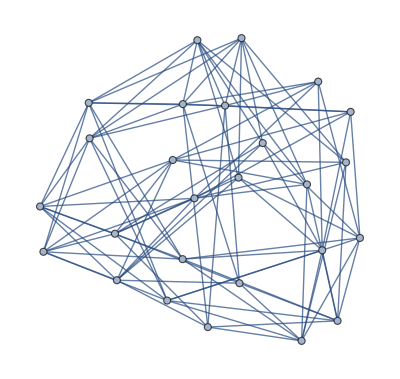

{{1,3,5,7,9,18,20,22,24,26}}

```mathematica
g=AdjacencyGraph[{{0,0,0,0,0,1,0,1,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0},{0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,1,0,1,0,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1},{0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0},{1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1},{0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,1,0},{0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,1,0,1,0,0},{0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,0,0,0},{1,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1},{0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0},{0,1,0,0,1,0,0,1,0,0,1,0,0,0,0,1,0,0,1,0,0,1,0,0,1,0},{1,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,1,1,0,0,0,1,0,0,0,1},{0,0,0,1,1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0,1,1,1,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,1,0,0,1,0,0,0,0,1,0,1,0,1,0,0},{0,1,0,1,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,1,0,1,0},{1,1,1,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,1,1,1},{0,1,0,0,0,1,0,0,0,1,0,0,0,0,0,0,1,0,0,0,1,0,0,0,1,0},{1,0,0,1,0,0,1,0,0,0,1,0,0,0,0,1,0,0,0,1,0,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,0,1,0,1,0,0,0,0,1,0,1,0,0,1,0,0,1,0,0},{0,0,0,1,0,0,0,1,0,1,0,0,0,0,0,0,1,0,1,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1,0,0,0,1,1,0,0,0,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,1,0,0,1,0,0,0,1,0,1,0,0,0,0,0}}]
FindIndependentVertexSet[g]
```

```mathematica
Length[{1,3,5,7,9,18,20,22,24,26}]
```

10